```mathematica
Quit[]
```

## GAP

### unflavored Schur index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-(1-x)^2/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+O[x]^16

### flavored Schur index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_,ξ_]:=1-((1-ξ x)(1-ξ^-1 x))/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i,ξ^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]//Simplify
```

1+(1+1/ξ^2+ξ^2) x^2-(2 (1+ξ^2) x^3)/ξ+((1+ξ^2+ξ^4)^2 x^4)/ξ^4-(2 (1+2 ξ^2+2 ξ^4+ξ^6) x^5)/ξ^3+(6+1/ξ^6+2/ξ^4+5/ξ^2+5 ξ^2+2 ξ^4+ξ^6) x^6-(2 ((1+ξ^2) (1+ξ^2+ξ^4)^2) x^7)/ξ^5+((1+ξ^2)^2 (1+5 ξ^4+3 ξ^6+5 ξ^8+ξ^12) x^8)/ξ^8-(2 (1+3 ξ^2+7 ξ^4+11 ξ^6+11 ξ^8+7 ξ^10+3 ξ^12+ξ^14) x^9)/ξ^7+((1+ξ^2+ξ^4)^2 (1+3 ξ^4+7 ξ^6+3 ξ^8+ξ^12) x^10)/ξ^10-(2 (1+3 ξ^2+8 ξ^4+16 ξ^6+23 ξ^8+23 ξ^10+16 ξ^12+8 ξ^14+3 ξ^16+ξ^18) x^11)/ξ^9+(68+1/ξ^12+2/ξ^10+6/ξ^8+16/ξ^6+35/ξ^4+57/ξ^2+57 ξ^2+35 ξ^4+16 ξ^6+6 ξ^8+2 ξ^10+ξ^12) x^12-(2 ((1+ξ^2+ξ^4)^2 (1+ξ^2+3 ξ^4+7 ξ^6+7 ξ^8+3 ξ^10+ξ^12+ξ^14)) x^13)/ξ^11+(131+1/ξ^14+2/ξ^12+6/ξ^10+16/ξ^8+37/ξ^6+73/ξ^4+113/ξ^2+113 ξ^2+73 ξ^4+37 ξ^6+16 ξ^8+6 ξ^10+2 ξ^12+ξ^14) x^14-1/ξ^13 2 (1+3 ξ^2+8 ξ^4+19 ξ^6+39 ξ^8+67 ξ^10+88 ξ^12+88 ξ^14+67 ξ^16+39 ξ^18+19 ξ^20+8 ξ^22+3 ξ^24+ξ^26) x^15+O[x]^16

### Junk

```mathematica
(*SnChar[n_,NN_]:=Module[{},
script="LoadPackage( \"ctbllib\" );;
	SnChar := function(n, N)
	\tlocal ct, irr, cp, short, part, sq, ans;
	\tct := CharacterTable(\"Symmetric\", n);;
	\tirr := Irr(ct);;
	\tcp := ClassParameters(ct);;
	\tshort := Filtered([1..Length(cp)], x->Length(cp[x][2]) <= N);;
	\tpart := List(cp, x -> x[2]);;
	\tsq := Sum(short, x -> irr[x] * irr[x]);;
	\tans := List([1..Length(part)], x -> [part[x], sq[x]]);;
	\tPrintTo(\"/Users/yinhslin/Downloads/index/output.txt\", ans);;
	end;;";
	script=script<>"
	SnChar("<>ToString[n]<>","<>ToString[NN]<>");;";

Export[NotebookDirectory[]<>"sym.txt",script];
DeleteFile[NotebookDirectory[]<>"sym.g"];
RenameFile[NotebookDirectory[]<>"sym.txt",NotebookDirectory[]<>"sym.g"];
gap="/Users/yinhslin/Downloads/gap-4.12.2/gap";
Run[gap<>" -q < "<>NotebookDirectory[]<>"sym.g"];

output=Import[NotebookDirectory[]<>"output.txt"];
output=StringReplace[output,{"["->"{","]"->"}"}]//ToExpression;
output
];*)
```

## GroupMath

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

### Sn characters complexity analysis

```mathematica
partitions=IntegerPartitions[30];
shortPartitions=Select[partitions,Length[#]<=5&];
```

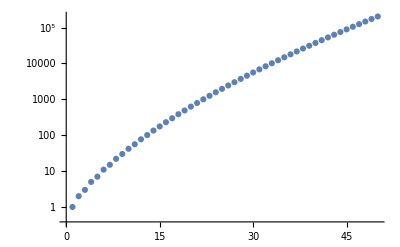

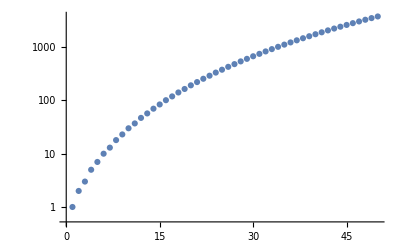

```mathematica
ListLogPlot[Table[Length[IntegerPartitions[n]],{n,1,50}]]
ListLogPlot[Table[Length[Select[IntegerPartitions[n],Length[#]<=5&]],{n,1,50}]]
```

### unrefined index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=18;
Series[Sum[index[2,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+3426 x^26+3152 x^27-13233 x^28+21336 x^29-18319 x^30-2994 x^31+40752 x^32-76884 x^33+78012 x^34-11808 x^35-121384 x^36+262206 x^37+O[x]^38

```mathematica
n=18;
Series[Sum[index[3,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+33 x^8-22 x^9+36 x^10+6 x^11-19 x^12+90 x^13-99 x^14+138 x^15-9 x^16-210 x^17+672 x^18-1116 x^19+1554 x^20-1270 x^21-36 x^22+2898 x^23-6705 x^24+10224 x^25-9918 x^26+2018 x^27+16470 x^28-42918 x^29+66906 x^30-66006 x^31+13566 x^32+106404 x^33-273204 x^34+407442 x^35-364710 x^36-12024 x^37+O[x]^38

### unflavored Schur index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-(1-x)^2/(1-x^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=16;
Series[(1+Sum[index[2,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+1269 x^16+O[x]^17

```mathematica
n=10;
Series[(1+Sum[index[7,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2+9 x^4+22 x^6+42 x^8+81 x^10+O[x]^11

## Mathematica built in FiniteGroupData

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
FiniteGroupData[{"SymmetricGroup",level},"CharacterTable"][[j,Length[partitions]-k+1]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
```

```mathematica
Series[Sum[index[2,i],{i,1,10}],{x,0,12}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11+81 x^12+O[x]^13

```mathematica
FiniteGroupData[{"SymmetricGroup",11},"CharacterTable"]
```

Missing[NotAvailable]

## Direct input

```mathematica
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
χ[shortPartitions[[j]],partitions[[k]]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
 χ[{1},{1}]=1;
 χ[{1,1},{1,1}]=1;
 χ[{1,1},{2}]=-1;
 χ[{2},{1,1}]=1;
χ[{2},{2}]=1;
χ[{1,1,1},{1,1,1}]=1;
χ[{1,1,1},{2,1}]=-1;
χ[{1,1,1},{3}]=1;
χ[{2,1},{1,1,1}]=2;
χ[{2,1},{2,1}]=0;
χ[{2,1},{3}]=-1;
χ[{3},{1,1,1}]=1;
χ[{3},{2,1}]=1;
χ[{3},{3}]=1;
```